## Oscillator disturbance rejection for uncertain frequency using optimal derivative control; statistics for J (Problem 9.7)

```mathematica
Clear["Global`*"];
```

```mathematica
μ=-1/2 Log[1+ϵ^2];σ=√Log[1+ϵ^2]; (* ϵ = normalized oscillator freq. uncertainty; avg=1 *)
Expectation[{1,ω},ω\[Distributed]LogNormalDistribution[μ,σ]]
```

{1,1}

```mathematica
jpdf[j_]:=√(2/π)1/(4σ)1/(j-k/4)ⅇ^(-1/(2 σ^2)(-1/2 Log[4k(j-k/4)]-μ)^2)
```

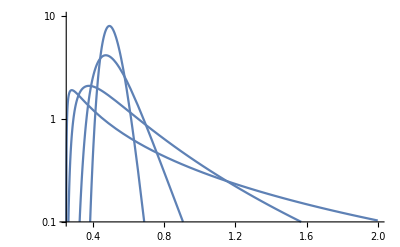

```mathematica
LogPlot[jpdf[j]/.{k->1,ϵ->{0.1,0.2,0.5,1}},{j,0,2},PlotRange->{0.1,10}]
```

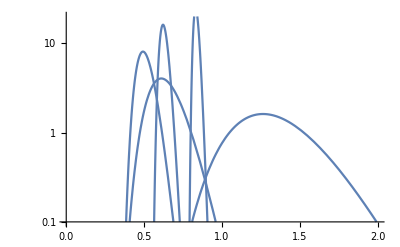

```mathematica
LogPlot[jpdf[j]/.{ϵ->0.1,k->{0.2,0.5,1,2,3}},{j,0,2},PlotRange->{0.1,20}]
```

```mathematica
j1=TransformedDistribution[1/4(k+1/(ω^2 k))/.k->1,ω\[Distributed]LogNormalDistribution[μ,σ]];
j1pdf=PDF[j1,jj]
```

Piecewise[{{(ⅇ^(-((Log[-1+4 jj]-Log[1+ϵ^2])^2)/(8 Log[1+ϵ^2])) √(2/π))/((-1+4 jj) √Log[1+ϵ^2]), jj>1/4&&√(-1+4 jj)>0}, {0, True}}]

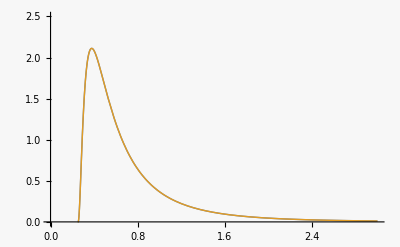

```mathematica
Plot[{jpdf[jj]/.{k->1,ϵ->0.5},j1pdf/.ϵ->0.5},{jj,0.25,3},PlotRange->{0,2.5}]  (* matches my hand-derived result!  *)
```

```mathematica
j1cdf=CDF[j1,jj]
```

Piecewise[{{1, jj>1/4&&1/(√(-1+4 jj))≤0}, {0, jj≤1/4}, {1/2 Erfc[(-Log[-1+4 jj]+Log[1+ϵ^2])/(2 √2 √Log[1+ϵ^2])], True}}]

```mathematica
jcdf=Integrate[jpdf[j],{j,j0,∞},Assumptions->{j0>k/4,ϵ>0,k>0}]
```

1/2 Erfc[Log[((4 j0-k) k)/(1+ϵ^2)]/(2 √2 √Log[1+ϵ^2])]

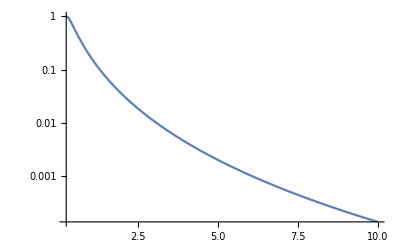

```mathematica
jcdf2=1/2 Erfc[(Log[(4 j0-k) k]+2μ)/(2 √2 σ)];
LogPlot[jcdf2/.{k->1,ϵ->0.5},{j0,1/4,10}]
```

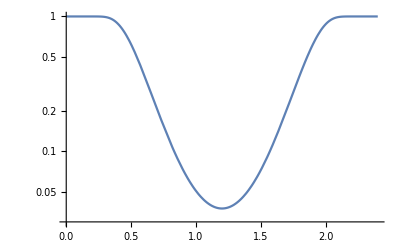

```mathematica
LogPlot[jcdf2/.{j0->0.6,ϵ->0.1},{k,0,4},PlotRange->{0.03,1}]
```